```mathematica
(*Weinberg's parameters*)
ep=0.08;β=0.7;γ=0.8;
τ=142.949;α=0.129692;γt=2.7536;
xmin=-50;xmax=50;maxtime=100; dd1=1;dd2=0.001;
(*Additional parameters*)
ρ=0.3;kappa=0.038;
(*γt=60;*)
(*Check condition on the parameters*)
eqn1=FindRoot[-v(1-v)(v-α)-(1+α-3v)ρ^2/2+v/γt,{v,0.9}];
v0=v/.eqn1
```

0.0962025

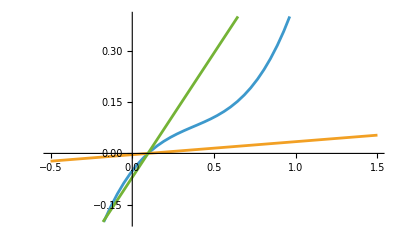

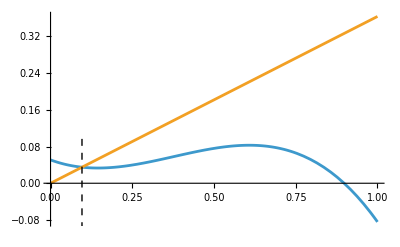

```mathematica
(*No linealindad original*)
g[x_,y_]=-x(1-x)(x-α)-(1+α-3x)ρ^2/2+y/γt;
Plot[{g[x,x],kappa(x-v0),2/γt(x-v0)},{x,-0.5,1.5},PlotRange->{-0.2,0.4}]
(*Graficos de las nulclinas*)
Show[Plot[{v(1-v)(v-α)+(1+α-3v)ρ^2/2,v/γt},{v,0,1}],Graphics[{Dashed,Line[{{v0,-0.1},{v0,0.1}}]}]]
```

InterpolatingFunction[…]

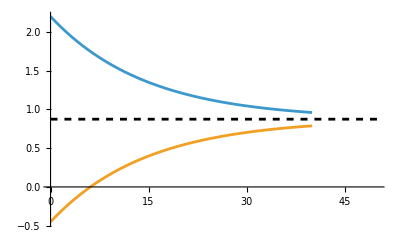

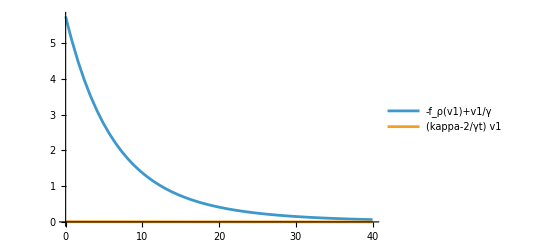

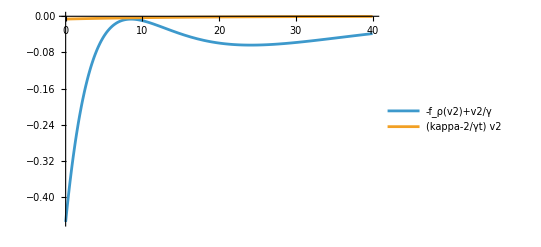

```mathematica
(*Buscamos el frente estacionario supersolucion*)
V0=NDSolveValue[{v''[x]==(kappa-2/γt) v[x],v[0]==2.2-v0,v'[0]==-Sqrt[kappa-2/γt](2.2-v0)},v,{x,0,40}]
Show[Plot[{V0[x]+v0,-V0[x]+v0},{x,0,40},PlotRange->All],Plot[v0,{x,0,xmax},PlotStyle->{Black,Dashed}]]
Plot[{g[v0+V0[x],v0+V0[x]],(kappa-2/γt) V0[x]},{x,0,40},PlotRange->All,PlotLegends->{"-f_ρ(v1)+v1/γ","(kappa-2/γt) v1"}]
Plot[{g[v0-V0[x],v0+V0[x]],(kappa-2/γt) (-V0[x])},{x,0,40},PlotRange->All,PlotLegends->{"-f_ρ(v2)+v2/γ","(kappa-2/γt) v2"}]
```

```mathematica
(*Comparing with the full system*)
a1[x_]=-α+Which[x<0,2v0(1+α)-3v0^2-3ρ^2/2,True,2v0(1+α)-3v0^2-3ρ^2/2];
a2[x_]=1+α+Which[x<0,0,True,-3v0];
{V1,W1}=NDSolveValue[{D[u[t, x], t] == D[u[t, x], x, x] +u[t,x](a1[x]+a2[x] u[t,x]-u[t,x]^2)- w[t,x],τ D[w[t,x],t]== 0.1(u[t, x] - γt w[t, x]), u[t, xmin] == 0, 
u[t, xmax] == 0,
u[0, x] ==0+Which[Abs[x+0]<5,1.15(5-Abs[x+0])/5,True,0],
 w[0, x] ==0/γ}, {u, w}, {t, 0, maxtime}, {x, xmin, xmax}];
(* u[t, x](1-u[t,x])(u[t,x]-α)+(1+α-3u[t,x])ρ^2/2
+NeumannValue[0,x==xmin]+NeumannValue[0,x==xmax]
*)
Animate[Show[Plot[V1[t,x],{x,xmin,xmax},PlotRange->{-1.5,1.5}],Plot[{V0[x],-V0[x]},{x,0,40},PlotRange->All,PlotStyle->Dashed],Plot[{2.2-v0,-(2.2-v0)},{x,xmin,0},PlotStyle->Dashed],Plot[0,{x,0,xmax},PlotStyle->{Black,Dashed}]],{t,0,maxtime,0.2},AnimationRunning->False]
```

NDSolveValue::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable x.